```mathematica
Clear["Global`*"];
r1[x1_,y1_] := {x1, y1};
r2[x2_,y2_] := {x2, y2};
(*define everything as functions of r1,r2 or t*)
r[x1_,y1_, x2_, y2_]:=Norm[r1[x1,y1]-r2[x2,y2]]
(*m is a mass matrix, not a vector*)
m=ArrayFlatten[{{m1*IdentityMatrix[2],{{0,0},{0,0}}},{ {{0,0},{0,0}},m2*IdentityMatrix[2]}}];
M11 := IdentityMatrix[2]/(6*π*η*a1);
(*(r1-r2)*(r1-r2) is suposed to be a dyadic product*)
(*I think you also had a typo in ((x1[t]-x2[t])*(x2[t]-x1[t]))*)
M12[x1_,y1_, x2_, y2_]:= 1/(8*π*η*r[x1,y1, x2,y2])*(IdentityMatrix[2]+1/r[x1,y1, x2,y2]^2 TensorProduct[(r1[x1,y1]-r2[x2,y2]),(r1[x1,y1]-r2[x2,y2])]);
M21[x1_,y1_, x2_, y2_] := 1/(8*π*η*r[x1,y1, x2,y2])*(IdentityMatrix[2]+TensorProduct[(r2[x2,y2]-r1[x1,y1]),(r2[x2,y2]-r1[x1,y1])]/r[x1,y1, x2,y2]^2);
(*M12[r1_,r2_]:= 1/(4*π*η*r[r1,r2]);*)
M22 := IdentityMatrix[2]/(6*π*η*a2);
M [x1_,y1_, x2_, y2_]:= ArrayFlatten[{{M11, M12[x1,y1,x2,y2]},{M21[x1,y1,x2,y2], M22}}];
F12[x1_,y1_, x2_, y2_,t_]:= Fa*Cos[2*π * f *t]*((r1[x1,y1]-r2[x2,y2])/r[x1,y1,x2,y2]);
F21[x1_,y1_, x2_, y2_, t_] := Fa*Cos[2*π * f *t]*((r2[x2,y2]-r1[x1,y1])/r[x1,y1,x2,y2]);
(*Fa, aka the force amplitude, was renamed (used to be called F) since it was coinciding with the general force function, also called F:*)
F [x1_,y1_, x2_, y2_,t_]:= Flatten[{F12[x1,y1,x2,y2,t], F21[x1,y1,x2,y2,t]}];
(**(x1[t]-x2[t])*)
G12[x1_,y1_, x2_, y2_]:=-k *(r [x1,y1,x2,y2]-L)*(r1[x1,y1]-r2[x2,y2])/r[x1,y1,x2,y2]; 
G21[x1_,y1_, x2_, y2_]:=-k *(r [x1,y1,x2,y2]-L)*(r2[x2,y2]-r1[x1,y1])/r[x1,y1,x2,y2]; 
G[x1_,y1_, x2_, y2_]:=Flatten[{G12[x1,y1,x2,y2], G21[x1,y1,x2,y2]}];
```

```mathematica
Clear["Global`*"];
(*define everything as functions of r1,r2 or t*)
r[r1_,r2_]:=Abs[r1-r2];
(*m is a mass matrix, not a vector*)
m={{m1,0},{ 0,m2}};
M11 [r1_,r2_]:= 1/(6*π*η*a1);
(*(r1-r2)*(r1-r2) is suposed to be a dyadic product*)
(*I think you also had a typo in ((x1[t]-x2[t])*(x2[t]-x1[t]))*)
M12[r1_,r2_]:= 1/(8*π*η*r[r1,r2])*(1+TensorProduct[(r1-r2),(r1-r2)]/r[r1,r2]^2);
(*M12[r1_,r2_]:= 1/(4*π*η*r[r1,r2]);*)
M22 [r1_,r2_]:= 1/(6*π*η*a2);
M [r1_,r2_]:= {{M11[r1,r2], M12[r1,r2]},{M12[r1,r2], M22[r1,r2]}};
F12[r1_,r2_,t_]:= Fa*Cos[2*π * f *t]*((r1-r2)/r[r1,r2]);
(*Fa, aka the force amplitude, was renamed (used to be called F) since it was coinciding with the general force function, also called F:*)
F [r1_,r2_,t_]:= {F12[r1,r2,t], -F12[r1,r2,t]};
(**(x1[t]-x2[t])*)
G1[r1_,r2_]:=-k *(r [r1,r2]-L)*(r1-r2)/r[r1,r2]; 
G2[r1_,r2_]:=-G1[r1,r2];
G[r1_,r2_]:={G1[r1,r2], G2[r1,r2]};
```

```mathematica
(*input paramters*)
a1 = 5;
a2 = 8;
η = 1/6;
f =0.2*10^-3;
Fa = 0.05;
k = 1/200;
L = 28;
ρs = 8;
m1 = 4/3*π*a1^3*ρs;
m2 = 4/3*π*a2^3*ρs;
(*τ is the period length*)
τ=1/f;
```

```mathematica
LHS[x1_,y1_,x2_,y2_] := Flatten[D[{{x1,y1},{x2,y2}},t]] 
RHS[x1_,y1_,x2_,y2_,t_] := M[x1, y1,x2,y2].(F[x1,y1,x2,y2,t]+G[x1,y1,x2,y2]-m.D[{x1,y1,x2,y2},{t,2}])
```

```mathematica
sol3 = NDSolve[{LHS[x1[t],y1[t],x2[t],y2[t]]==RHS[x1[t],y1[t],x2[t],y2[t],t],(*{x1[t],y1[t],x2[t],y2[t]},*) { x1[0],y1[0],x2[0],y2[0]}=={-L,5,0,5}, { x1'[0],y1'[0],x2'[0],y2'[0]}=={0,0,0,0}},{x1,y1,x2,y2},{t,0.01,100τ}, Method->{"EquationSimplification"->"Residual"}]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],x2→InterpolatingFunction[…],y2→InterpolatingFunction[…]}}

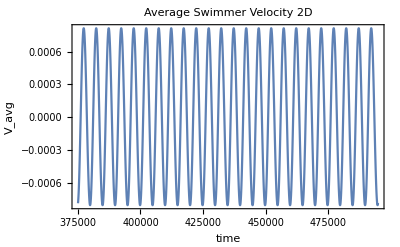

```mathematica
Plot[Evaluate[{(x1'[t]+x2'[t])/2}/.sol3],{t,75τ, 99τ},PlotRange->All, AxesStyle->Black,Frame->True,FrameStyle->Black,PlotLabel->Style["Average Swimmer Velocity 2D", Black], FrameLabel->{"time","V_avg"}]
```

```mathematica
sol=NDSolve[{{r1'[t], r2'[t]}==M[r1[t],r2[t]].(F[r1[t],r2[t],t]+G[r1[t],r2[t]]-m.{r1''[t],r2''[t]}),{ r1[0],r2[0]}=={-L,0}, { r1'[0],r2'[0]}=={0,0}}, {r1, r2}, {t, 0,100τ}]
```

{{r1→InterpolatingFunction[…],r2→InterpolatingFunction[…]}}

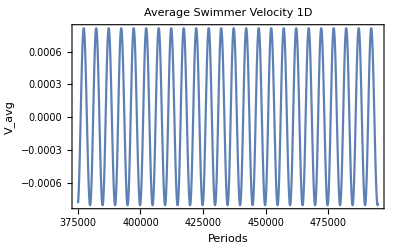

```mathematica
Plot[Evaluate[{(r1'[t]+r2'[t])/2}/.sol],{t,75τ, 99τ},PlotRange->All, AxesStyle->Black,Frame->True,FrameStyle->Black,PlotLabel->Style["Average Swimmer Velocity 1D", Black], FrameLabel->{"time","V_avg"}]
```

```mathematica
NIntegrate[Evaluate[1/τ*{(Norm[{x1'[t],y1'[t]}]+Norm[{x2'[t],y2'[t]}])/2}/.sol3],{t,98τ,99τ}]
```

{{0.00109542}}